```mathematica
SetDirectory[NotebookDirectory[]];
file1  ="jobsHistory_10_AMJ_31Jan_000.xlsx";
file2  ="jobsHistory_10_AMJ_31Jan_766.xlsx";
file3  ="jobsHistory_10_AMJ_31Jan_866.xlsx";
file4  ="jobsHistory_10_AMJ_31Jan_151212.xlsx";
file5  ="jobsHistory_10_AMJ_31Jan_131212.xlsx";
```

## Functions

```mathematica
Main functions-per job;
```

```mathematica
findSlavesTasks [listTasks_]:= Module[{},GatherBy[SortBy[MapThread[{#1, #2}&,{listTasks,Range@Length@listTasks}],First],#[[1]]&][[#]][[All,2]] &/@Range@CountDistinct@listTasks]
paramJobBySlave2[Location_,param_,jobNum_]:= Module[{},ToExpression@paramJob[Location,param,jobNum,"Slaves"] ]
```

```mathematica
updateTask[uniSlaves_,slavesNum_]:=Module[{missingNodes,rangeNumbers,nodes},
missingNodes = slavesNum- Length@uniSlaves;
nodes=ToExpression[StringTake[#,-1]&/@uniSlaves];
 rangeNumbers=If [slavesNum == 3,Range[1,5,2],Range[5]];
Flatten@Position[MemberQ[nodes,#]&/@rangeNumbers,False]
]
```

```mathematica
addZeros[reducersList_,slavesNum_,list_,zeroReg_]:=Module[{distinictNodes,toUpdateIndex,zer},
distinictNodes = CountDistinct@reducersList;
zer = If[zeroReg =="list",{0},0];
If[ distinictNodes== slavesNum,list,toUpdateIndex=updateTask [Union@reducersList,slavesNum];
Flatten[Insert[list,zer,#]&/@toUpdateIndex,1] ]
]
```

```mathematica
plotGraphsPerF[location_,firstJ_,lastJ_,f_,p_]:=Module[{},
Switch[p,
1,Table[plotReducersAloocationJobs[location[[i]],"Box Aloocation","",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
 2,Table[plotAllJobs[location[[i]],"Shuffle","Box",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
3,Table[plotAllJobs[location[[i]],"Shuffle","Mean",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
4,Table[plotAllJobs[location[[i]],"Shuffle","Variance",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
 5,Table[plotAllJobs[location[[i]],"Elapsed","Box",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
6,Table[plotAllJobs[location[[i]],"Elapsed","Mean",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
7,Table[plotAllJobs[location[[i]],"Elapsed","Variance",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
8,Table[plotAllJobs[location[[i]],"Total Input","Box",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
9,Table[plotAllJobs[location[[i]],"Total Input","Mean",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
10,Table[plotAllJobs[location[[i]],"Total Input","Variance",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}], 
11,Table[plotAllJobs[location[[i]],"Input","Box",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
12,Table[plotAllJobs[location[[i]],"Input","Mean",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
13,Table[plotAllJobs[location[[i]],"Input","Variance",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
14,Table[plotParamJobs[location[[i]],"C",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
15,plotParamJobs2[location,"C","Box",firstJ[[1]],lastJ[[1]],f],
16,plotParamJobs2[location,"C","Mean",firstJ[[1]],lastJ[[1]],f],
17,plotParamJobs2[location,"C","Variance",firstJ[[1]],lastJ[[1]],f],
18,Table[plotAllJobs[location[[i]],"Total Groups","Pie",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
19,Table[plotAllJobs[location[[i]],"Groups","Pie",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
(*20,Table[plotAllJobs[location[[i]],"Total Groups","Box",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],*)
(*1,Table[plotReducersAloocationJobs[location[[i]],"","",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],*)
(* 3,Table[plotReducersAloocationJobs[location[[i]],"","Variance",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],*)
 21,Table[plotByJob[location[[i]],"Shuffle",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
 22,Table[plotByJob[location[[i]],"Elapsed",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
 23,Table[plotByJob[location[[i]],"Input",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
24,Table[plotByJob[location[[i]],"Total Input",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
25,Table[plotByJob[location[[i]],"Total Groups",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
26,Table[plotReducersAloocationJobs[location[[i]],"Aloocation","",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
27,Table[plotAllJobs[location[[i]],"MergeReduce","Box",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}],
28,Table[plotAllJobs[location[[i]],"MergeReduce","Mean",firstJ[[i]],lastJ[[i]],f[[i]]],{i,Length@location}]
]
]
```

```mathematica
plotAllGraphs[location_,f_,fRrounds_,lRrounds_]:=Module[{},
Table[Print@plotGraphsPerF[location,ConstantArray[fRrounds,Length@location],ConstantArray[lRrounds,Length@location],f,i],{i,1,1}];(* Reducers Aloocation *)
Table[Print@plotGraphsPerF[location,ConstantArray[fRrounds,Length@location],ConstantArray[lRrounds,Length@location],f,i],{i,2,3}];(* Shuffle Time *)
Table[Print@plotGraphsPerF[location,ConstantArray[fRrounds,Length@location],ConstantArray[lRrounds,Length@location],f,i],{i,27,28}];(* Merge + Reduce Time *)
Table[Print@plotGraphsPerF[location,ConstantArray[fRrounds,Length@location],ConstantArray[lRrounds,Length@location],f,i],{i,5,6}];(* Reducers Elapsed *)
(*Print@Text@Style["Reducers Total Input",Blue,Italic,50];
Table[Print@plotGraphsPerF[location,ConstantArray[1,Length@location],ConstantArray[rounds,Length@location],f,i],{i,8,10}];*)
Table[Print@plotGraphsPerF[location,ConstantArray[fRrounds,Length@location],ConstantArray[lRrounds,Length@location],f,i],{i,11,12}];(* Reducers Input *)
(*Table[Print@plotGraphsPerF[location,ConstantArray[1,Length@location],ConstantArray[rounds,Length@location],f,i],{i,18,19}]; *)
Table[Print@plotGraphsPerF[location,ConstantArray[fRrounds,Length@location],ConstantArray[lRrounds,Length@location],f,i],{i,18,18}];(* Groups *)
Table[Print@plotGraphsPerF[location,ConstantArray[fRrounds,Length@location],ConstantArray[lRrounds,Length@location],f,i],{i,14,17}];(* Completion Time *)
Table[Print@plotGraphsPerF[location,ConstantArray[fRrounds,Length@location],ConstantArray[lRrounds,Length@location],f,i],{i,21,22}];(* ByJob *)

]
```

```mathematica
paramJob[Location_,param_,jobNum_,mode_]:= Module[{sheetNum= jobNum+1,job ,MappersSize, reducersSize,reducersList, reducersListParam, reduceTasksBySlave,seekParam , distinictNodes,slavesNum=3,toUpdateIndex,amount},
job= Import[Location,{"Sheets",sheetNum}];
reducersSize=ToExpression[Import[Location,{"Sheets",1,sheetNum}][[7]]];
MappersSize = ToExpression[Import[Location,{"Sheets",1,sheetNum}][[4]]];
reducersList = Transpose[job[[(-reducersSize);;]]][[3]];
(*Print@reducersList;*)
seekParam=Switch[ param ,"Shuffle",4,"Elapsed",2,"Input",8,"Total Input",8,"Groups",11,"Total Groups",11,"Merge",5,"Reduce",6];
Switch[mode,"Tasks",Transpose[job[[-reducersSize;;]]][[seekParam]],"ReducersAloocation",amount=Tally[Sort@reducersList][[All,2]];addZeros[reducersList,slavesNum,amount,"num"],"Slaves",
reduceTasksBySlave=findSlavesTasks [reducersList];
reducersListParam =If [ param =="MergeReduce",ToExpression[Transpose[job[[(#+2+MappersSize)]]][[5]]&/@reduceTasksBySlave ]+ToExpression[ Transpose[job[[(#+2+MappersSize)]]][[6]]&/@reduceTasksBySlave ],Transpose[job[[(#+2+MappersSize)]]][[seekParam]]&/@reduceTasksBySlave];
addZeros[reducersList,slavesNum,reducersListParam,"list"]
(*distinictNodes = CountDistinct@reducersList;
If[ distinictNodes== slavesNum,reducersListParam,toUpdateIndex=updateTask [Union@reducersList,slavesNum];
Flatten[Insert[reducersListParam,{0},#]&/@toUpdateIndex,1] ]
*)
]
]
```

```mathematica
plotAllJobs[Location_,param_,plotType_,firstJ_,lastJ_,dVec_]:= Module[{paramBySlaveAllJobs, allSlavesParam,medianVarParam,fLabel,pLabel,pRange,places={"Virginia","California","London"},plSize =24,flSize =16,clSize1 =20,clSize2 =18,legenedSize=16,tickSize =16},
paramBySlaveAllJobs =paramJobBySlave2[Location,param,#]&/@Range[firstJ,lastJ];
allSlavesParam =If[param  =="Total Input" || param  =="Total Groups",Transpose@Table[Map[Total,paramBySlaveAllJobs[[i]]],{i,Length@paramBySlaveAllJobs}], Flatten[#,1]&/@Transpose@paramBySlaveAllJobs];
medianVarParam = Switch[plotType,"Pie",N@Mean@# &/@allSlavesParam,"Mean",N@Mean@# &/@allSlavesParam, "Variance",N@Variance@# &/@allSlavesParam,_,allSlavesParam];
fLabel ={"",Text[Style["Sec",FontSize->flSize]]};
pLabel = Text[Style[StringJoin[ToString@param,StringJoin[" time, ",dVec]],FontSize->plSize]];
pRange=Switch[plotType,
"Pie",Switch[param,"Groups",{Automatic,{0,100}},"Total Groups",{Automatic,{0,100}}],
"Box",Switch[param,"Shuffle",{Automatic,{0,250}},"MergeReduce",{Automatic,{0,150}},"Elapsed",{Automatic,{0,350}},"Input",{Automatic,{0,1100}},"Total Input",{Automatic,{0,1300}}],"Groups",{Automatic,{0,10000}},
"Mean",Switch[param,"Shuffle",{Automatic,{0,200}},"MergeReduce",{Automatic,{0,70}},"Elapsed",{Automatic,{0,250}},"Input",{Automatic,{0,700}},"Total Input",{Automatic,{0,1100}}],
"Variance",Switch[param,"Shuffle",{Automatic,{0,3100}},"MergeReduce",{Automatic,{0,4400}},"Elapsed",{Automatic,{0,4400}},"Input",{Automatic,{0,3600}},"Total Input",{Automatic,{Automatic,Automatic}}] ] ;
If[param == "Input" || param == "Total Input",medianVarParam=N[medianVarParam/1000000];fLabel ={"",Text[Style["MB",FontSize->flSize]]};pLabel =StringJoin[plotType, Text[Style[StringJoin[" shuffled data per region, ",dVec]]],FontSize->plSize]];
Switch[plotType, "Box",BoxWhiskerChart[medianVarParam,{"Mean",{"Fences",1,Black}}, Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize, PlotLabel->pLabel,PlotRange->pRange, PlotTheme->{"ItalicLabels"},ChartStyle->"BrightBands",ChartLabels->places,ImageSize->Large],
"Pie",PieChart[N[medianVarParam/96],PlotLabel->pLabel,PlotTheme->{"ItalicLabels"},ChartStyle->"BrightBands",ChartLabels->places,ImageSize->Large],
_,BarChart[medianVarParam, Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize,PlotLabel->pLabel,PlotRange->pRange, PlotTheme->{"ItalicLabels"},ChartStyle->"BrightBands",ChartLabels->Text[Style[#,FontSize->clSize2]]&/@places,ImageSize->Large]  ]
]
```

```mathematica
plotByJob[Location_,param_,firstJ_,lastJ_,dVec_]:= Module[{jobs,numJobs,statPerJob,paramBySlaveAllJobs,jobLables,fLabel,pLabel,pRange,Isize,places={"Virginia","California","London"},plSize =24,flSize =20,clSize1 =24,clSize2 =20,legenedSize=22,tickSize =16},
(*jobs = Import[Location,"Sheets"];(*show all sheets*)numJobs = Length@jobs -1;*)
paramBySlaveAllJobs =paramJobBySlave2[Location,param,#]&/@Range[firstJ,lastJ];
Table[Table[If[Length@paramBySlaveAllJobs[[i,j]] ==1,paramBySlaveAllJobs[[i,j]]=Flatten@Append[paramBySlaveAllJobs[[i,j]],paramBySlaveAllJobs[[i,j]] ] ] ,{j,3}],{i,Length@paramBySlaveAllJobs}];(* duplicate lonley reducers *)
paramBySlaveAllJobs =If[param  =="Total Input" || param =="Total Groups",Table[Map[Total,paramBySlaveAllJobs[[i]]],{i,Length@paramBySlaveAllJobs}],Table[Mean@N@#&/@paramBySlaveAllJobs[[i]],{i,Length@paramBySlaveAllJobs}]];
(* Flatten[#,1]&/@Transpose@paramBySlaveAllJobs]; *)
fLabel ={"",Text[Style["Sec",FontSize->flSize]]};
pLabel =Text[Style[Switch[param,"Input",StringJoin["Shuffled data, ",dVec],"Total Input",StringJoin["Total shuffled data, ",dVec],"Total Groups",StringJoin["Groups #, ",dVec],_,StringJoin["Reducers ",StringJoin[ToString@param,StringJoin[" time- ",dVec]]]   ] ,FontSize->plSize]];
jobLables=StringJoin["Job ",IntegerString@#]&/@Range[firstJ,lastJ];
(* pRange=Automatic; pRange={Automatic,{Automatic,Max@Flatten@paramBySlaveAllJobs }}{0,8 *10^8}} *)
 pRange=Switch[param,"Shuffle",{Automatic,{0,370}},"Elapsed",{Automatic,{0,370}},"Input",{Automatic,{0,1100}},"Total Input",{Automatic,{0,2200}},"Total Groups",{Automatic,{0,10000}}];
Isize = 1400;
If[param == "Input" || param == "Total Input",paramBySlaveAllJobs=N[paramBySlaveAllJobs/1000000];fLabel ={"",Text[Style["MB",FontSize->flSize]]}];
If[param == "Groups",fLabel={"","# groups"}];
BarChart[paramBySlaveAllJobs, Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize,(*PlotLabel->pLabel,*)PlotRange->pRange, PlotTheme->{"ItalicLabels"},ChartLegends->Placed[Text[Style[#,FontSize->legenedSize]]&/@places,{Left,Top}],ChartStyle->RegionsPlatte,ChartLabels->{Text[Style[#,FontSize->clSize2]]&/@jobLables,{"","",""}},Epilog->{Switch[dVec,"Non-Adaptive",nonAdaptiveColor,"Adaptive",AdaptiveColor],Text[Style[dVec,FontSize->clSize1,Bold],{15,-15},{0,0}]},ImageSize->Large](*,
BoxWhiskerChart[paramBySlaveAllJobs,{"Mean",{"Fences",1,Black}}, Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize, PlotLabel->pLabel,PlotRange->pRange, PlotTheme->{"ItalicLabels"},ChartLegends->Placed[{"Virginia","California","London"},{Left,Top}],ChartStyle->"BrightBands",ChartLabels->{jobLables,{"1","2","3"}},ImageSize->Large]*)
]
```

```mathematica
plotParamJobs[Location_,param_,firstJ_, lastJ_,dVec_] := Module[{statJobs, seekParam, jobLables,data,fLabel,pLabel,pRange,plSize =24,flSize =16,clSize1 =20,clSize2 =18,legenedSize=16,tickSize =16},
  statJobs =  Import[Location, {"Sheets", 1}];
  (*ElapsedTime, AVGShuffle, NodeAM *)
 seekParam=Switch[ param ,"C",2,"Shuffle",10,"AM",22];
 data = ToExpression[Transpose[statJobs][[seekParam, 2 ;;]]]; 
data = data [[firstJ;;lastJ]];
  jobLables=StringJoin["Job ",IntegerString@#]&/@Range[firstJ,lastJ]; 
fLabel ={"",Text[Style["Sec",FontSize->flSize]]};
pLabel = Text[Style[StringJoin["Jobs-Completion Time, ",dVec],FontSize->plSize]];
pRange= {Automatic,{0,350}};
 BarChart[data,  Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize,PlotLabel->pLabel,PlotRange->pRange,PlotTheme->{"ItalicLabels"},ChartLabels ->Text[Style[#,FontSize->clSize2]]&/@jobLables,ImageSize->Large] 
    ]
```

```mathematica
plotParamJobs2[Location_,param_,plotType_,firstJ_, lastJ_,dVec_] := Module[{statJobs, seekParam, jobLables,data,fLabel,pLabel,pRange,plSize =24,flSize =20,clSize1 =24,clSize2 =18,legenedSize=16,tickSize =16},
  statJobs =  Import[Location, {"Sheets", 1}];
  (*ElapsedTime, AVGShuffle, NodeAM *)
 seekParam=Switch[ param ,"C",2,"Shuffle",10,"AM",22];
data = ToExpression[Transpose[Import[#, {"Sheets", 1}] [[firstJ;;lastJ]] ][[seekParam, 2 ;;]]]&/@Location ;
fLabel ={"",Text[Style["Sec",FontSize->flSize]]};
pLabel = Text[Style["Jobs-Completion Time",FontSize->plSize]];
 Switch[plotType, "Box",(* pRange={Automatic,{0,350}}; *) pRange={Automatic,{0,350}};BoxWhiskerChart[data,{"Mean",{"Fences",1,Black}}, Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize,(*PlotLabel->pLabel,*)PlotRange->pRange,ChartLabels->{ Text[Style["Non-Adaptive",FontSize->clSize1]],Text[Style["Adaptive",FontSize->clSize1]]},ChartStyle->{nonAdaptiveColor,AdaptiveColor}, PlotTheme->{"ItalicLabels"},ImageSize->Large],
"Mean",data = N@Mean@#&/@data ;(*pRange={Automatic,{0,250}};*)pRange={Automatic,{0,300}}; pLabel = Text[Style[StringJoin[plotType," Jobs-Completion Time"],FontSize->plSize]];BarChart[data,  Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize,PlotLabel->pLabel,PlotRange->pRange,PlotTheme->{"ItalicLabels"},ChartLabels -> Text[Style[#,FontSize->clSize2]]&/@dVec,ImageSize->Large] ,
"Variance",data = N@Variance@#&/@data ;(* pRange={Automatic,{0,2200}}; *) pRange={Automatic,{0,2100}}; pLabel = Text[Style[StringJoin[plotType," Jobs-Completion Time"],FontSize->plSize]];BarChart[data,  Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize,PlotLabel->pLabel,PlotRange->pRange,PlotTheme->{"ItalicLabels"},ChartLabels -> Text[Style[#,FontSize->clSize2]]&/@dVec,ImageSize->Large]  ]
]
```

```mathematica
plotReducersAloocationJobs[Location_,param_,VarAVG_,firstJ_, lastJ_,dVec_]:=Module[{paramBySlaveAllJobs,fLabel,pLabel,pRange,jobLables,places={"Virginia","California","London"},plSize =24,flSize =16,clSize1 =20,clSize2 =18,legenedSize=16,tickSize =16},
paramBySlaveAllJobs =ToExpression@paramJob[Location,param,#,"ReducersAloocation"]&/@Range[firstJ,lastJ];
paramBySlaveAllJobs = If[VarAVG == "Variance",N@Variance[#]&/@Transpose[paramBySlaveAllJobs],paramBySlaveAllJobs];
fLabel ={"",Text[Style["Amount",FontSize->flSize]]};
 pLabel = Text[Style[ If[VarAVG == "Variance",StringJoin[VarAVG,StringJoin[" # Reducers ",dVec]],StringJoin["# Reducers ",dVec]],FontSize->plSize]];;
pRange=If[VarAVG == "Variance",{Automatic,{0,0.3}},{Automatic,{0,8}}];
If[param =="Box Aloocation",BoxWhiskerChart[Transpose@paramBySlaveAllJobs, Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize, PlotLabel->pLabel,PlotRange->pRange, PlotTheme->{"ItalicLabels"},ChartLabels -> Text[Style[#,FontSize->clSize2]]&/@places,ChartStyle->"BrightBands",ImageSize->Large],
jobLables=StringJoin["Job ",IntegerString@#]&/@Range[firstJ,lastJ];
BarChart[paramBySlaveAllJobs, Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize, PlotLabel->pLabel,PlotRange->pRange, PlotTheme->{"ItalicLabels"},ChartLegends->Placed[Text[Style[#,FontSize->legenedSize]]&/@places,{Left,Top}],ChartStyle->"BrightBands",ChartLabels->{Text[Style[#,FontSize->clSize2]]&/@jobLables,{"","",""}},ImageSize->Large] ]
]
```

```mathematica
Final comparing functions;
```

```mathematica
places2={"Virginia","California","London"};
places={"US East","US West","EU"};
plot6Comparing[locations_,fRrounds_,lRrounds_,downlinks_]:=Module[{},
Print@compareReducerInput[locations,fRrounds,lRrounds,downlinks];
Print@stackReducerTimes[locations,fRrounds,lRrounds,downlinks];
Print@ plotBoxPlots[locations,fRrounds,lRrounds];
Print@compareC[locations,fRrounds,lRrounds,downlinks];
Print@plotParamJobs2[locations,"C","Box",fRrounds,lRrounds,downlinks];
Print@ Table[plotByJob[locations[[i]],"Elapsed",fRrounds,lRrounds,downlinks[[i]]],{i,Length@locations}];
]
```

```mathematica
(*
 nonAdaptiveColor= ORcolor[173,31,255];
stackReducerPlatte= {ORcolor[119,162,255],ORcolor[255,119,137],ORcolor[255,244,119]};
RegionsPlatte={ORcolor[58,229,255],ORcolor[68,58,255],ORcolor[58,255,91]};
RegionsPlatte={ORcolor[255,122,95],ORcolor[255,162,95],ORcolor[255,95,122]};
stackReducerPlatte= {ORcolor[255,152,136],ORcolor[154,255,208],ORcolor[255,141,208]};
AdaptiveColor=ORcolor[255,218,31];

nonAdaptiveColor= ORcolor[145,0,255];
AdaptiveColor=ORcolor[255,196,0];
*)
averageColor =ORcolor[3,52,83];
nonAdaptiveColor= Black;
AdaptiveColor=Black;
```

```mathematica
compareReducerInput[Locations_,firstJ_,lastJ_,dVec_]:= Module[{paramBySlaveAllJobs, allSlavesParam,medianVarParam,fLabel,pLabel,pRange,color={nonAdaptiveColor,AdaptiveColor},plSize =24,flSize =30,clSize1 =24,clSize2 =19,legenedSize=20,tickSize =16},
paramBySlaveAllJobs =Table[paramJobBySlave2[Locations[[i]],"Input",#]&/@Range[firstJ,lastJ],{i,Length@Locations}];
allSlavesParam = Table[Flatten[#,1]&/@Transpose@paramBySlaveAllJobs[[i]],{i,Length@Locations}];
medianVarParam = Table[N[(Mean@#)/1000000] &/@allSlavesParam[[i]],{i,Length@Locations}];
pRange={Automatic,{0,700}};
fLabel ={"",Text[Style["MB",FontSize->flSize]]};
BarChart[medianVarParam, Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize,(*PlotLabel->Text[Style["Shuffled data",FontSize->plSize]],*)PlotRange->pRange ,PlotTheme->{"ItalicLabels"},ChartStyle->regionsPlatte,ChartLabels -> {" "(*Table[Text[Style[dVec[[i]],FontSize->clSize1,FontColor->color[[i]] ,Bold] ],{i,Length@dVec}] ,*)Text[Style[#,FontSize->clSize2]]&/@places},BarSpacing->{Automatic,Medium},(*ChartElements->{Graphics[{Blue,Thick,Line[{{0,0},{0.5,0.05}}]}],Automatic,Automatic,Automatic,Automatic,Automatic},*)ImageSize->Large,
Epilog->{{nonAdaptiveColor,Text[Style["Non-Adaptive",FontSize->clSize1,Bold],{2.3,-75},{0,0}]},{AdaptiveColor,Text[Style["Adaptive",FontSize->clSize1,Bold],{5.65,-75},{0,0}]}}]  
]
```

```mathematica
loopMeanReduceTime[Locations_,param_,firstJ_,lastJ_,dVec_]:= Module[{paramBySlaveAllJobs, allSlavesParam,meanVarParam},
paramBySlaveAllJobs =ToExpression@Table[paramJobBySlave2[Locations[[i]],param,#]&/@Range[firstJ,lastJ],{i,Length@Locations}];
allSlavesParam = Table[Flatten[#,1]&/@Transpose@paramBySlaveAllJobs[[i]],{i,Length@Locations}];
meanVarParam = Flatten@Table[N@Mean@# &/@allSlavesParam[[i]],{i,Length@Locations}]
]
```

```mathematica
stackReducerTimes[Locations_,firstJ_,lastJ_,dVec_]:= Module[{data,fLabel,pLabel,pRange,plSize =24,flSize =30,clSize1 =24,clSize2 =18,legenedSize=22,tickSize =16},
data = loopMeanReduceTime[Locations,#,firstJ,lastJ,dVec]&/@{"Shuffle","Merge","Reduce"};
pRange={Automatic,{0,250}};
fLabel ={"",Text[Style["Sec",FontSize->flSize]]};
data= Insert[Transpose@data,{0},4] ;
BarChart[data, Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize,(*PlotLabel->Text[Style["Reducers phases time",FontSize->plSize]],*)PlotRange->pRange,ChartLegends->Placed[Text[Style[#,FontSize->legenedSize]]&/@{"Shuffle","Merge","Reduce"},{Right,Top}],ChartStyle->stackReducerPlatte,ChartLabels -> {Text[Style[#,FontSize->clSize2]]&/@{"Virginia","California","London","","Virginia","California","London"},{"","",""}},PlotTheme->{"ItalicLabels"},Epilog->{{nonAdaptiveColor,Text[Style["Non-Adaptive",FontSize->clSize1,Bold],{2,-25},{0,0}]},{AdaptiveColor,Text[Style["Adaptive",FontSize->clSize1,Bold],{6,-25},{0,0}]}},ChartLayout->"Stacked",ImageSize->Large]  
]
```

```mathematica
prepareBoxData[Location_,firstJ_, lastJ_]:=Module[{reducersTime, dataperJob, jobLables,data,mean,max},
  reducersTime =paramJobBySlave2[Location,"Elapsed",#]&/@Range[firstJ,lastJ];
data=Transpose@reducersTime;
data=Flatten[#,1]&/@data;
dataperJob =Table[Mean@#&/@reducersTime[[i]],{i,Length@reducersTime}];
 mean =Mean@N@#&/@dataperJob; 
max=Max@#&/@dataperJob;
(* data= Insert[Insert[data,mean,-1],max,-1] *)
data=Insert[data,max,-1]
]
plotBoxPlots[Locations_,firstJ_, lastJ_] := Module[{reducersTime, mean, chartPallete,data,bc,fLabel,pLabel,pRange,chartLab,chartLab2,plSize =50,flSize =30,clSize1 =24,clSize2 =20,legenedSize=16,tickSize =16},
data=Join[{prepareBoxData[Locations[[1]],firstJ, lastJ]},{prepareBoxData[Locations[[2]],firstJ, lastJ]}];
fLabel ={"",Text[Style["Sec",FontSize->flSize]]};
pLabel = Text[Style["Jobs-Completion Time",FontSize->plSize]];
pRange={{1,All},{100,350}};
(* chartLab= {Text[Style[#,FontSize->clSize2]]&/@Insert[Insert[places,"Average",-1],"Straggler",-1]}; *)
chartLab= {Text[Style[#,FontSize->clSize2]]&/@Insert[places,"Straggler",-1]};
chartLab2= {Text[Style[#,FontSize->clSize1,Bold]]&/@{"Non-Adaptive","Adaptive"}};
chartPallete=Join[Insert[{boxesPlotPlatte},boxesPlotPlatte,-1]];
BoxWhiskerChart[data,{"Mean",{"Fences",1,Black}}, Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize,(*PlotLabel->pLabel,*)PlotRange->pRange,
ChartLabels ->Join[chartLab2,chartLab],ChartStyle->chartPallete,
BarSpacing->{Medium,Large},(* Epilog->{{nonAdaptiveColor,Text[Style["Non-Adaptive",FontSize->clSize1,Bold],{2,-2},{5,10}]},{AdaptiveColor,Text[Style["Adaptive",FontSize->clSize1,Bold],{6,-25},{0,0}]}} ,*) 
PlotTheme->{"ItalicLabels"},ImageSize->Large]]
```

```mathematica
compareC[Locations_,firstJ_, lastJ_,dVec_] := Module[{statJobs, jobLables,data,fLabel,pLabel,pRange={Automatic,{0,350}},plSize =24,flSize =20,clSize1 =20,clSize2 =22,legenedSize=16,tickSize =16},
  statJobs =  Transpose@Import[#, {"Sheets", 1}]&/@Locations;
 data = ToExpression[#[[2, 2 ;;]]&/@statJobs]; 
data = # [[firstJ;;lastJ]] &/@data;
jobLables=StringJoin["Job ",IntegerString@#]&/@Range[firstJ,lastJ];
fLabel ={"",Text[Style["Sec",FontSize->flSize]]};
 BarChart[Transpose[Sort@#&/@data],  Frame->{{True,False},{True,False}},FrameLabel->fLabel,FrameTicksStyle->tickSize,(*PlotLabel->Text[Style["Jobs-Completion Time",FontSize->plSize]],*)PlotRange->pRange,PlotTheme->{"ItalicLabels"},ChartLegends->Placed[Text[Style[#,FontSize->legenedSize]]&/@dVec,{Left,Top}],ChartStyle->{nonAdaptiveColor,AdaptiveColor},ChartLabels -> {Text[Style[#,FontSize->clSize2]]&/@jobLables,{"",""}},ImageSize->Large] 
    ]
```

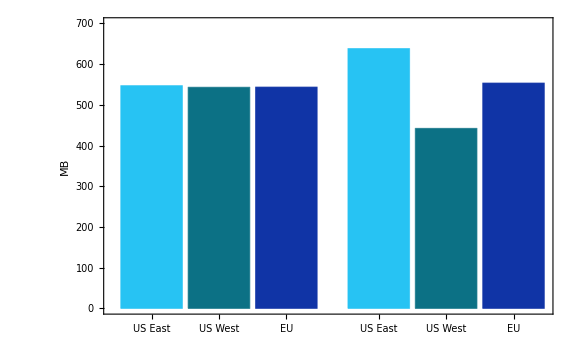

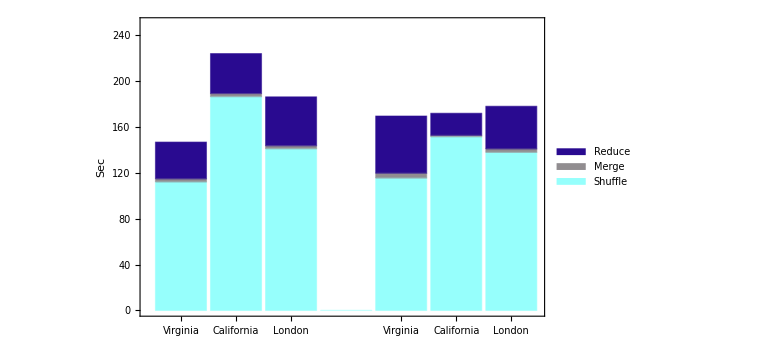

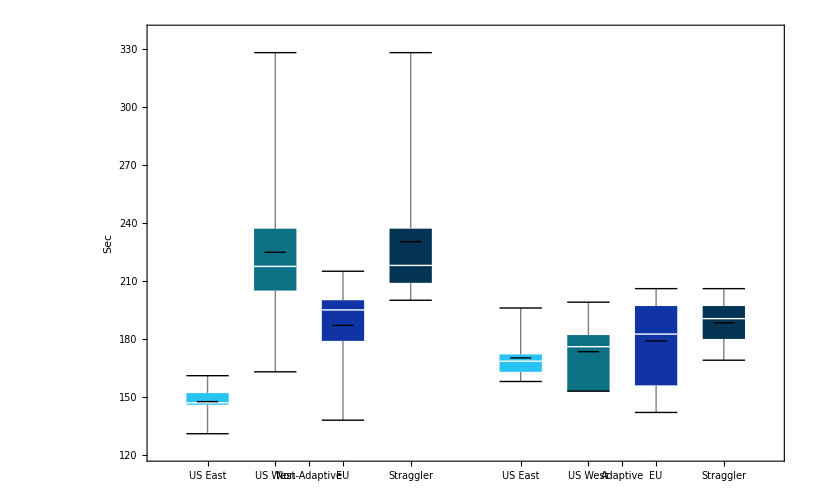

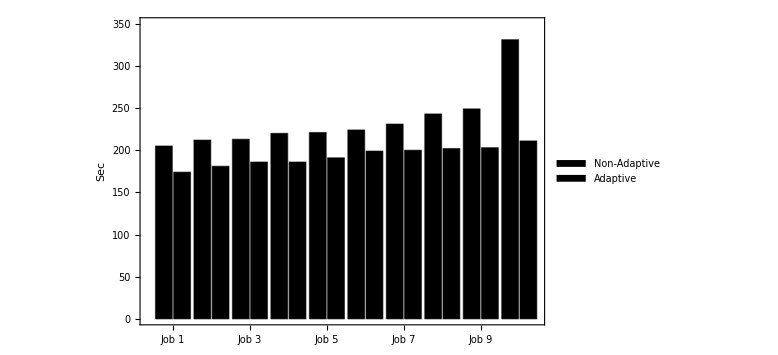

Import::chtype: First argument {jobsHistory_10_AMJ_31Jan_000.xlsx,jobsHistory_10_AMJ_31Jan_766.xlsx} is not a valid file, directory, or URL specification.

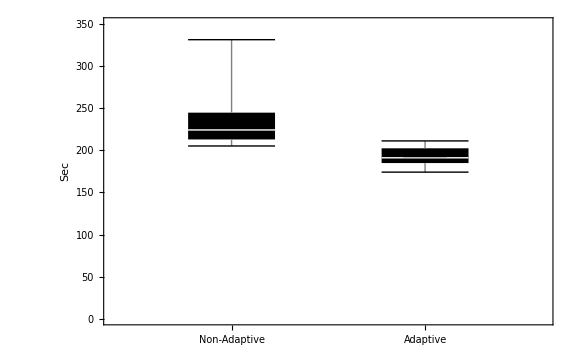

BarChart::chsty: Value of option ChartStyle -> RegionsPlatte is not a style or group of styles.

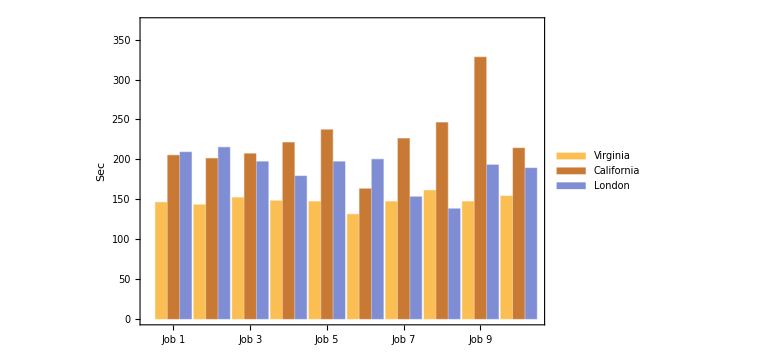
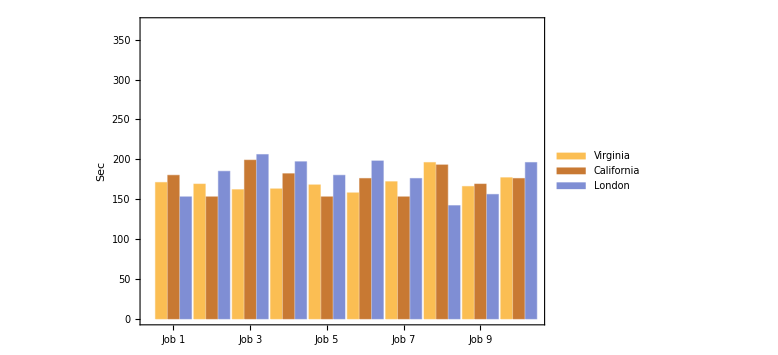

```mathematica
ORcolor[r_,g_,b_]:=Module[{},RGBColor[r/255,g/255,b/255]]
bluePlatte1={ORcolor[39,195,243],ORcolor[12,113,133],ORcolor[16,52,166],ORcolor[3,52,83]};
bluePlatte2={ORcolor[150,255,252],ORcolor[145,141,144],ORcolor[41,10,144],ORcolor[80,179,255]};
bluePlatte3={ORcolor[31,255,248],ORcolor[78,163,186],ORcolor[78,173,250],ORcolor[74,109,224],ORcolor[16,16,232]};
bluePlatte4={ORcolor[78,173,250],ORcolor[74,109,224],ORcolor[12,113,133],ORcolor[16,52,166],ORcolor[3,52,83]};
greenPlatte= {ORcolor[178,255,63],ORcolor[96,240,166],ORcolor[65,255,12],ORcolor[105,148,105]};
redPlatte= {ORcolor[255,145,112],ORcolor[204,90,77],ORcolor[255,47,43],ORcolor[194,16,0]};
yellowPlatte= {ORcolor[218,230,108],ORcolor[255,242,0],ORcolor[255,191,15],ORcolor[255,157,0]};

regionsPlatte=bluePlatte1;
stackReducerPlatte=bluePlatte2;
boxesPlotPlatte= bluePlatte1;
plot6Comparing[{file1,file2},1,10,{"Non-Adaptive","Adaptive"}]
```

{jobsHistory_10_AMJ_31Jan_000.xlsx,jobsHistory_10_AMJ_31Jan_766.xlsx}

{f= 0 0 0,f= 7 6 6}

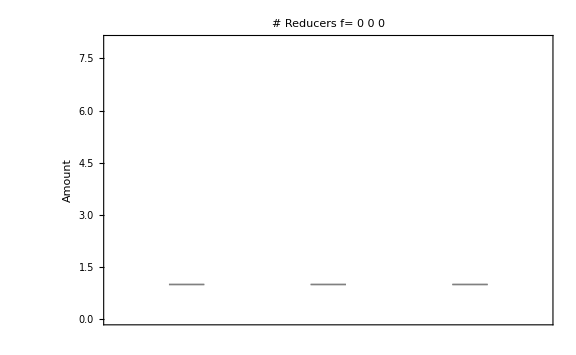
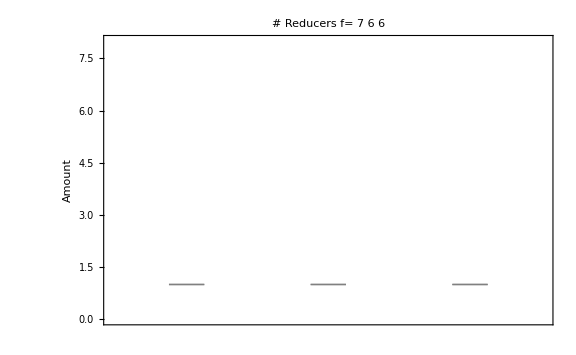

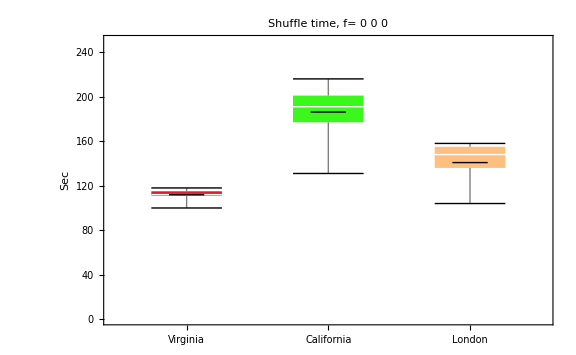
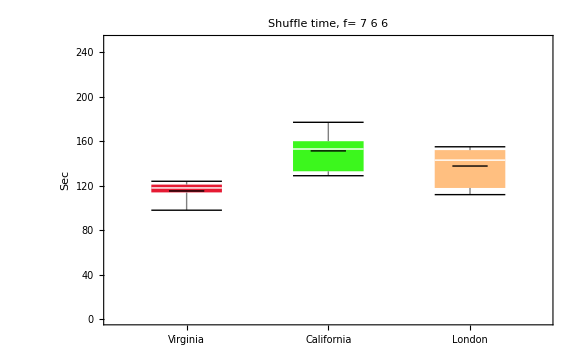

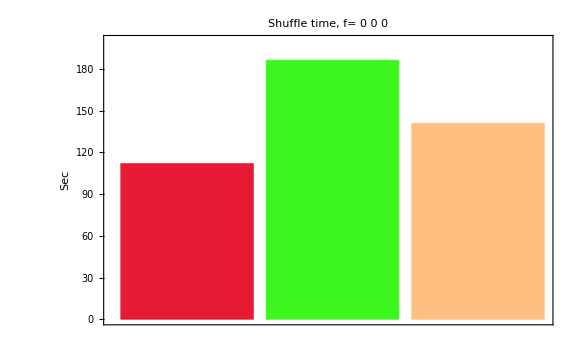
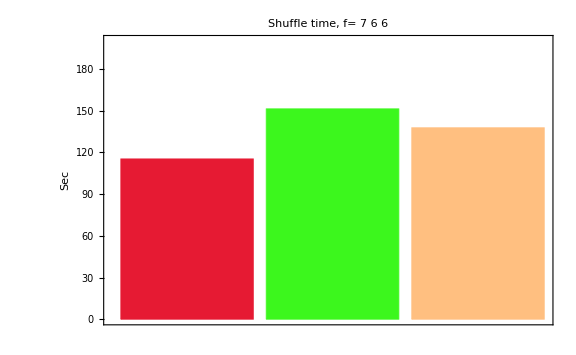

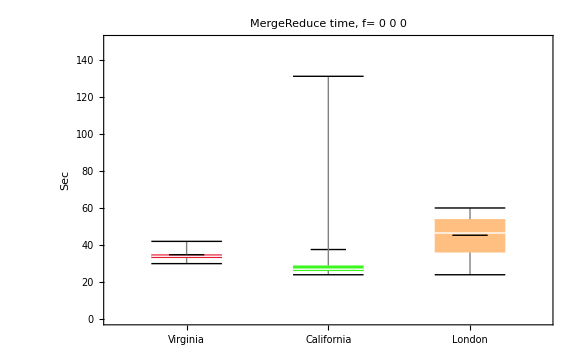
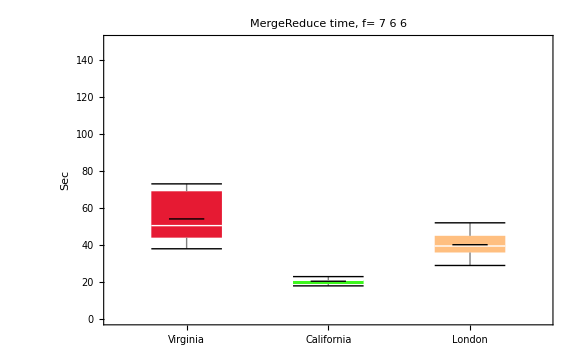

StringJoin::string: String expected at position 2 in Box<> shuffled data per region, f= 0 0 0<>(FontSize→24).

StringJoin::string: String expected at position 3 in Box<> shuffled data per region, f= 0 0 0<>(FontSize→24).

StringJoin::string: String expected at position 2 in Box<> shuffled data per region, f= 7 6 6<>(FontSize→24).

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

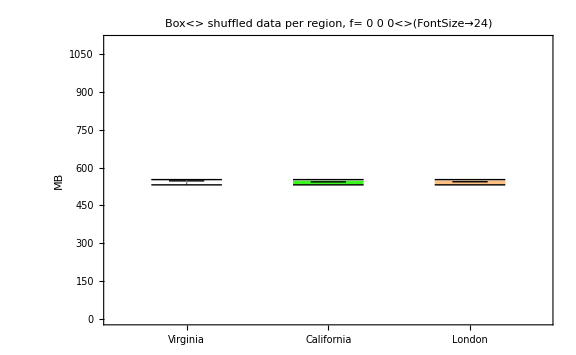
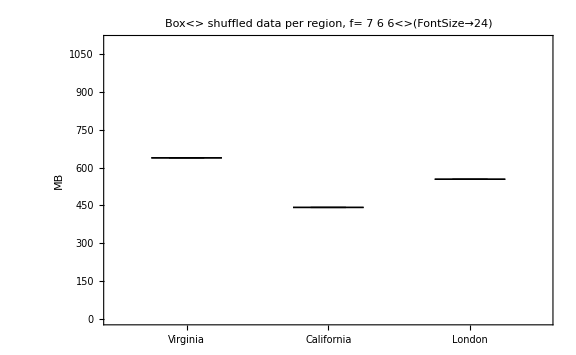

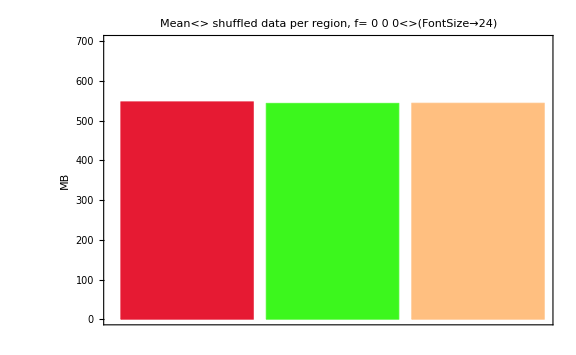
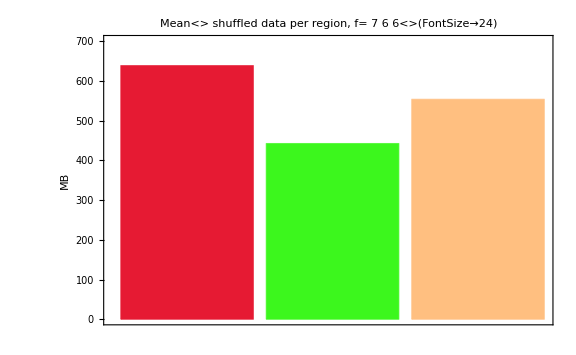

{-Graphics-,-Graphics-}

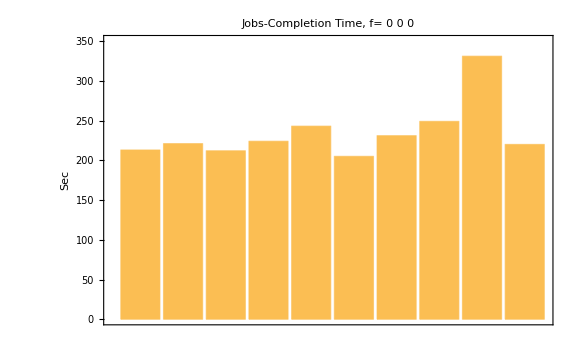
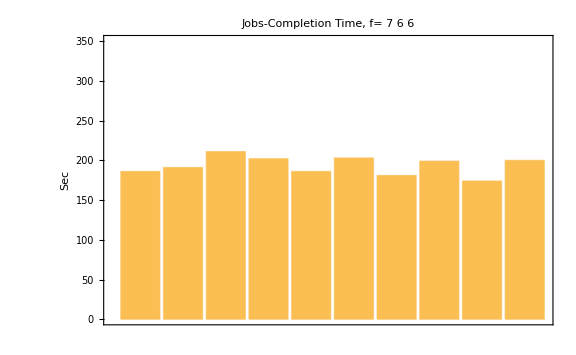

Import::chtype: First argument {jobsHistory_10_AMJ_31Jan_000.xlsx,jobsHistory_10_AMJ_31Jan_766.xlsx} is not a valid file, directory, or URL specification.

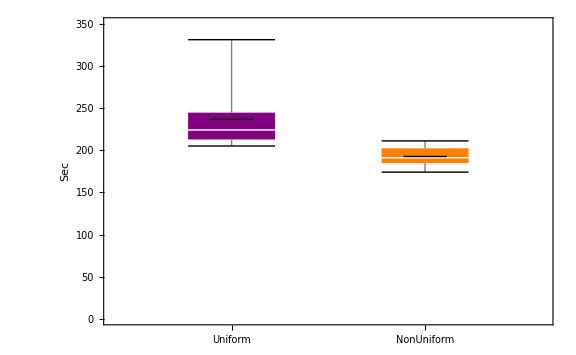

Import::chtype: First argument {jobsHistory_10_AMJ_31Jan_000.xlsx,jobsHistory_10_AMJ_31Jan_766.xlsx} is not a valid file, directory, or URL specification.

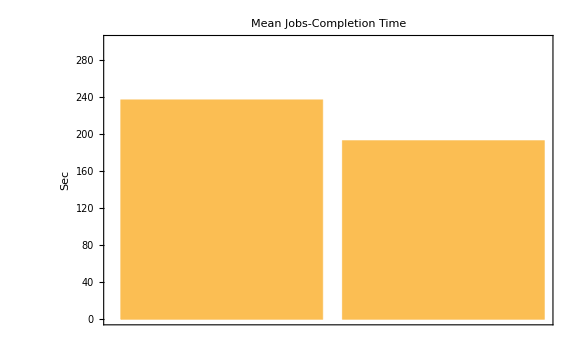

Import::chtype: First argument {jobsHistory_10_AMJ_31Jan_000.xlsx,jobsHistory_10_AMJ_31Jan_766.xlsx} is not a valid file, directory, or URL specification.

General::stop: Further output of Import::chtype will be suppressed during this calculation.

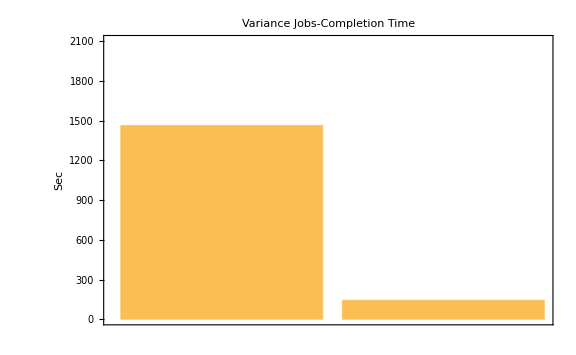

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

RGBColor[0, 0.5, 0.5]

```mathematica
files401 ={file1,file2}(*,file24,file34,file44,file54};*)
f1= {"f= 0 0 0","f= 7 6 6"}(*,"f= 8 6 6","f= 15 12 12","f= 13 12 12","f= 9 6 8"};*)
plotAllGraphs[files401,f1,1,10]
```